```mathematica
f1 = E^(-(x-1)^2/ϵ)
```

ⅇ^(-(-1+x)^2/ϵ)

General::munfl: Exp[-999.918] is too small to represent as a normalized machine number; precision may be lost.

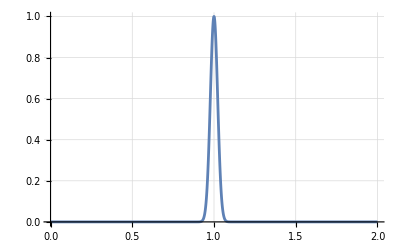

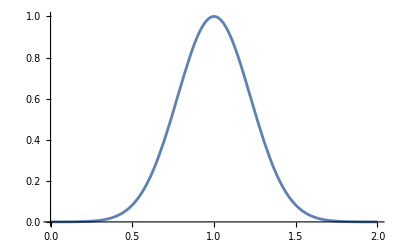

```mathematica
subst = ϵ->1*^-3;
Plot[f1/.subst, {x, 0, 2}, PlotRange->All, GridLines->Automatic]
```

```mathematica
intF1 = Integrate[f1/.subst, x]
intf1 = Integrate[f1/.subst, {x,0,2}]
%//N
```

1/200 √(π/10) Erf[100 √10 (-1+x)]

1/100 √(π/10) Erf[100 √10]

0.00560499

```mathematica
a = intF1/.x->0//N
b = intF1/.x->2;
b - a//N
```

-1.30701×10^171

1.30701×10^171

```mathematica
Erfi[10 √5 (-2+x)/.x->2]//N
```

0.

```mathematica
f2 = x Sin[1/x]
```

x Sin[1/x]

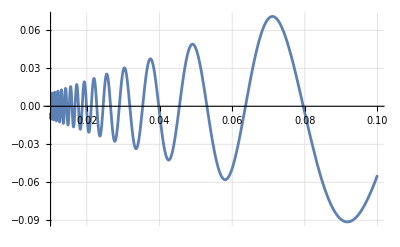

```mathematica
Plot[f2, {x, 1/100, 1/10}, GridLines->Automatic]
```

```mathematica
intF2 = Integrate[f2, x]
```

1/2 x Cos[1/x]+1/2 x^2 Sin[1/x]+1/2 SinIntegral[1/x]

```mathematica
SinIntegral[10]/2//N
```

0.829174

```mathematica
f31 = 2x+5
f32 = (-5 π^2(x^2-2x-5)+10π x+2x)/(1+5 π^2)
f33 = 2Sin[2x] + (4 + 20 π^2+25 π^3)/(π + 5 π^3)-2Sin[4/π]
```

5+2 x

(2 x+10 π x-5 π^2 (-5-2 x+x^2))/(1+5 π^2)

(4+20 π^2+25 π^3)/(π+5 π^3)-2 Sin[4/π]+2 Sin[2 x]

Piecewise[{{5+2 x, 0≤x<1/π}, {(2 x+10 π x-5 π^2 (-5-2 x+x^2))/(1+5 π^2), 1/π≤x<2/π}, {(4+20 π^2+25 π^3)/(π+5 π^3)-2 Sin[4/π]+2 Sin[2 x], 2/π≤x≤8/π}, {0, True}}]

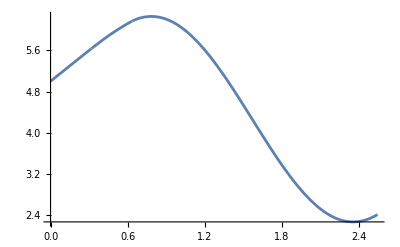

```mathematica
f3 = Piecewise[{{f31, 0<=x<1/π}, {f32, 1/π <=x<2/π}, {f33, 2/π<=x<=8/π}}]
Plot[f3, {x,0,8/π }, GridLines->Automatic]
```

```mathematica
Integrate[f31, x]
Integrate[f32, x]
Integrate[f33, x]
```

5 x+x^2

(25 π^2 x+x^2+5 π x^2+5 π^2 x^2-(5 π^2 x^3)/3)/(1+5 π^2)

((4+20 π^2+25 π^3) x)/(π+5 π^3)-Cos[2 x]-2 x Sin[4/π]

```mathematica
Integrate[f3, {x, 0, 8/π}]
%//N
```

(84+25 π+420 π^2+600 π^3+3 π^2 Cos[4/π]+15 π^4 Cos[4/π]-3 π^2 Cos[16/π]-15 π^4 Cos[16/π]-36 π Sin[4/π]-180 π^3 Sin[4/π])/(3 π^2 (1+5 π^2))

11.6391